```mathematica
distis=Import[NotebookDirectory[]<>"veneto.txt","table","FieldSeparators"->";","NumberPoint"->","];
```

```mathematica
distis[[1;;10]]//TableForm
```

Name | Origine | Destinazione | Total_Minu | Total_Mete
1042 - 23059 | 1042. | 23059. | 129.69 | 243791.
1042 - 23022 | 1042. | 23022. | 131.86 | 246794.
1042 - 23082 | 1042. | 23082. | 133.84 | 253807.
1042 - 23083 | 1042. | 23083. | 136.44 | 252085.
1042 - 23043 | 1042. | 23043. | 136.47 | 251192.
1042 - 23089 | 1042. | 23089. | 136.52 | 251738.
1042 - 23015 | 1042. | 23015. | 138.58 | 259000.
1042 - 23057 | 1042. | 23057. | 138.75 | 255266.
1042 - 23096 | 1042. | 23096. | 140.26 | 259813.

```mathematica
distisPad = Select[distis,#[[3]] == 28060.&];
distisPadAss = AssociationThread[Round[distisPad[[All,2]]]->distisPad[[All,4;;5]]];
```

```mathematica
padovaCityEnti=CityData["Padua"][[1]];

knownRegs={"Abruzzes","Apulia","Basilicata","Calabria","Campania","EmiliaRomagna","FriuliVeneziaGiulia","Lazio","Liguria","Lombardy","Marche","Molise","Piemonte","Sardegna","Sicily","Toscana","TrentinoAltoAdige","Umbria","ValleDAosta","Veneto"};
regEntis=Entity["AdministrativeDivision",{#,"Italy"}]&/@knownRegs;

provEntis=#["Subdivisions"]&/@regEntis;
knownProvs=Map[CanonicalName[#][[1]]&,provEntis,{2}];
findProvByName[real_]:=Module[{editDists},
editDists=Map[EditDistance[#,real]&,knownProvs,{2}];
{regID,provID}=FirstPosition[editDists,Min[editDists]];
Return[{regID,provID}];]
```

```mathematica
commEntis=Map[#["Subdivisions"]&,provEntis,{2}];
knownComms=Map[CanonicalName[#][[1]]&,commEntis,{3}];
findCommByName[real_]:=Module[{editDists},
editDists=Map[EditDistance[#,real]&,knownComms,{3}];
{regID,provID,commID}=FirstPosition[editDists,Min[editDists]];
Return[{regID,provID,commID}];]
```

### Top 20 visitor countries

```mathematica
dayOdD=Import[NotebookDirectory[]<>"distinct_users_day.csv"];
dayOdD[[1;;10]]//TableForm;
```

```mathematica
foreignDayOdD=Select[dayOdD,#[[2]]=="foreigner"&];
perCountryAss=Reverse@Sort[Total[#[[All,6]]]&/@GroupBy[foreignDayOdD, #[[3]]&]];
```

```mathematica
countryCodes=Import[NotebookDirectory[]<>"codici_nazioni_edit.csv"];
countryCodes[[1;;5]]//TableForm;
countryAss=AssociationThread[countryCodes[[All,1]]->countryCodes[[All,2]]];
```

```mathematica
topCountries =Partition[Riffle[Keys[perCountryAss],Values[perCountryAss]],2][[1;;20]];
```

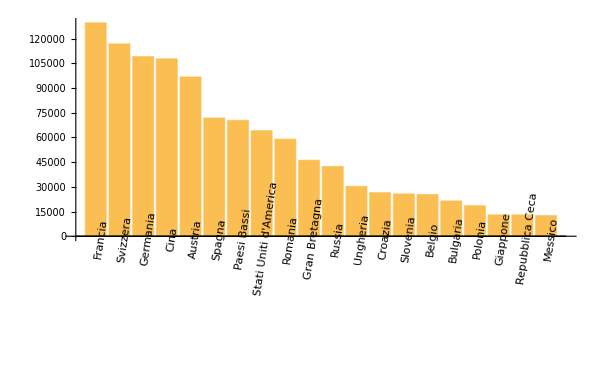

```mathematica
BarChart[topCountries[[All,2]], ChartLabels->Placed[topCountries[[All,1]]/.countryAss,Axis,Rotate[#,Pi/2.2]&], ImageSize->600]
```

### Italian visitors

```mathematica
italianDayOdD=Select[dayOdD,#[[2]]=="visitor"&];
perProvAss=Total[#[[All,6]]]&/@GroupBy[italianDayOdD, #[[4]]&];
```

```mathematica
provCodes=Import[NotebookDirectory[]<>"codici_istat_provincia.csv"];
provCodes[[1;;-1]]//TableForm;
provNamesAss=AssociationThread[provCodes[[All,2]]->provCodes[[All,3]]];
AppendTo[provNamesAss,""->Style["Unknown",Red]];
```

```mathematica
perProvs =Partition[Riffle[Keys[perProvAss],Values[perProvAss]],2];
niceProvs=Select[perProvs,!NumberQ[#[[1]]/.provNamesAss] && #[[1]] ≠ ""&];
```

```mathematica
provCorrections={"Venezia"->"Venice","Valle d'Aosta/Vallée d'Aoste"->"Aosta"};
provPopsAss=#[[1]]->With[{ij=findProvByName[#[[1]]/.provNamesAss/.provCorrections]},QuantityMagnitude@Extract[provEntis,ij]["Population"]]&/@niceProvs;
provPopsAss[[1;;5]]//TableForm
```

35→517316
22→538579
52→266621
108→859044
29→244062

```mathematica
Export[NotebookDirectory[]<>"provPops.txt",Transpose[{Keys[provPopsAss],Values[provPopsAss]}], "Table"];
```

```mathematica
topProvs=Reverse[SortBy[{#[[1]], N[#[[2]]/(#[[1]]/.provPopsAss)],#[[1]]/.provPopsAss}&/@niceProvs,#[[2]]&]][[1;;20]];
```

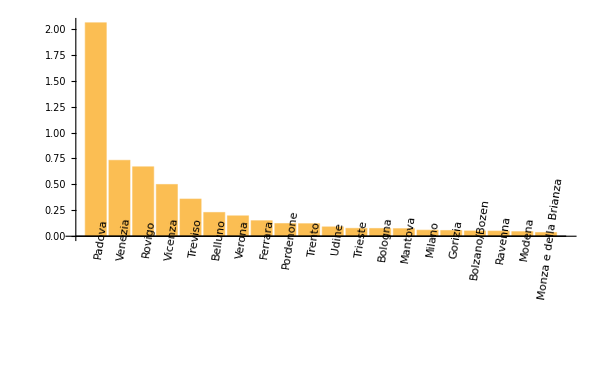

```mathematica
bc=BarChart[topProvs[[All,2]], ChartLabels->Placed[topProvs[[All,1]]/.provNamesAss,Axis,Rotate[#,Pi/2.2]&], ImageSize->600]
```

```mathematica
Extract[commEntis,findCommByName[#[[1]]/.commNamesAss]]["Position"]&/@perComm
```

perComm

### Highway visitors

```mathematica
commCodes=Import[NotebookDirectory[]<>"codici_istat_comune.csv"];
commCodes[[1;;-1]]//TableForm;
commNamesAss=AssociationThread[commCodes[[All,2]]->commCodes[[All,3]]];
AppendTo[commNamesAss,""->Style["Unknown",Yellow]];
```

```mathematica
dayOd=Import[NotebookDirectory[]<>"day_od_edit.csv"];
dayOd[[1;;5]]//TableForm
italianDayOd21=Select[dayOd,#[[5]]=="visitor"&& #[[8]]≠-999 && Quotient[#[[3;;4]],100 ]== {2,1}&];
italianDayOd21[[1;;10]]//TableForm
```

MONTH | DOW | ORIGIN | DESTINATION | CUST_CLASS | COD_COUNTRY | COD_PRO | PRO_COM | FLOW
Marzo | Domenica | 108 | 300 | visitor | 222 | 28 | -999 | 493
Maggio | Lunedì | 300 | 101 | visitor | 222 | 93 | -999 | 58
Febbraio | Sabato | 108 | 207 | visitor | 222 | 28 | -999 | 39
Aprile | Venerdì | 109 | 121 | resident | 222 | 28 | 28060 | 106

Febbraio | Giovedì | 207 | 102 | visitor | 222 | 28 | 28086 | 173
Febbraio | Sabato | 216 | 106 | visitor | 222 | 28 | 28103 | 46
Febbraio | Domenica | 218 | 125 | visitor | 222 | 28 | 28016 | 40
Aprile | Martedì | 206 | 126 | visitor | 222 | 28 | 28001 | 111
Maggio | Martedì | 203 | 121 | visitor | 222 | 28 | 28066 | 39
Marzo | Venerdì | 206 | 101 | visitor | 222 | 28 | 28001 | 170
Marzo | Giovedì | 216 | 106 | visitor | 222 | 28 | 28103 | 67
Aprile | Venerdì | 217 | 101 | visitor | 222 | 28 | 28100 | 151
Maggio | Giovedì | 212 | 105 | visitor | 222 | 28 | 28048 | 57
Maggio | Mercoledì | 218 | 118 | visitor | 222 | 28 | 28016 | 1190

```mathematica
italianDayOd21//Length
```

9474

```mathematica
isWeekend[day_]:=(day =="Sabato" || day == "Domenica") 
{italianDayOd21WD,italianDayOd21WE}=GatherBy[italianDayOd21,isWeekend[#[[2]]]&];
Length@italianDayOd21WD
Length@italianDayOd21WE
```

7226

2248

```mathematica
perCommWD ={#[[1,1]],Total@#[[All,2]]}&/@GatherBy[italianDayOd21WD[[All,{8,9}]],#[[1]]&];
perCommWE ={#[[1,1]],Total@#[[All,2]]}&/@GatherBy[italianDayOd21WE[[All,{8,9}]],#[[1]]&];
```

```mathematica
refPos =padovaCityEnti["Position"]
angleVisitsWD={#[[1]]/.commNamesAss,QuantityMagnitude@GeoDirection[refPos, Extract[commEntis,findCommByName[#[[1]]/.commNamesAss]]["Position"]],#[[2]]}&/@perCommWD;
angleVisitsWE={#[[1]]/.commNamesAss,QuantityMagnitude@GeoDirection[refPos, Extract[commEntis,findCommByName[#[[1]]/.commNamesAss]]["Position"]],#[[2]]}&/@perCommWE;
angleVisitsWE//TableForm
(*angleVisitsWE//TableForm*)
```

GeoPosition[{45.41,11.87}]

Villafranca Padovana | -38.6792 | 5534
Cadoneghe | 35.3483 | 18676
Albignasego | -178.779 | 34151
Abano Terme | -133.098 | 9796
Selvazzano Dentro | -99.0045 | 16883
Vigodarzere | 2.27954 | 22781
Ponte San Nicolò | 142.079 | 23984
Casalserugo | 162.358 | 3467
Maserà di Padova | 179.544 | 3449
Saonara | 112.471 | 7362
Noventa Padovana | 87.3377 | 18084
Rubano | -59.7503 | 22426
Stra | 89.2691 | 1316
Vigonza | 61.0606 | 12192
Montegrotto Terme | -144.602 | 2774
Campodarsego | 22.8977 | 539
Limena | -19.8872 | 4269
Legnaro | 134.134 | 3109
Mestrino | -61.5634 | 4487
Vigonovo | 100.301 | 2603
Fiesso d'Artico | 83.6172 | 361
Milano | -87.2561 | 36
Pianiga | 67.9765 | 764
Due Carrare | -165.066 | 875
Saccolongo | -90.5772 | 992
Polverara | 149.642 | 138
Terni | 168.306 | 32
Grisignano di Zocco | -57.9823 | 32

```mathematica
angleVisits2WD=SortBy[{#[[1]],-Mod[#[[2]],360]/180*Pi+Pi/2,#[[3]]}&/@angleVisitsWD,#[[2]]&];
angleTicksWD = Select[angleVisits2WD,#[[3]]>50000&][[All,{2,1}]]
angleVisits2WE=SortBy[{#[[1]],-Mod[#[[2]],360]/180*Pi+Pi/2,#[[3]]}&/@angleVisitsWE,#[[2]]&];
angleTicksWE = Select[angleVisits2WE,#[[3]]>10000&][[All,{2,1}]]
```

{{-3.66955,Rubano},{-2.98443,Selvazzano Dentro},{-1.59211,Albignasego},{-0.908953,Ponte San Nicolò},{0.0464659,Noventa Padovana},{0.953852,Cadoneghe},{1.53101,Vigodarzere}}

{{-3.66955,Rubano},{-2.98443,Selvazzano Dentro},{-1.59211,Albignasego},{-0.908953,Ponte San Nicolò},{0.0464659,Noventa Padovana},{0.505089,Vigonza},{0.953852,Cadoneghe},{1.53101,Vigodarzere}}

PolarAxes::polarticks: Value of PolarTicks -> angleTicks[0,2 π] should be None, Automatic, or a list of tick specifications.

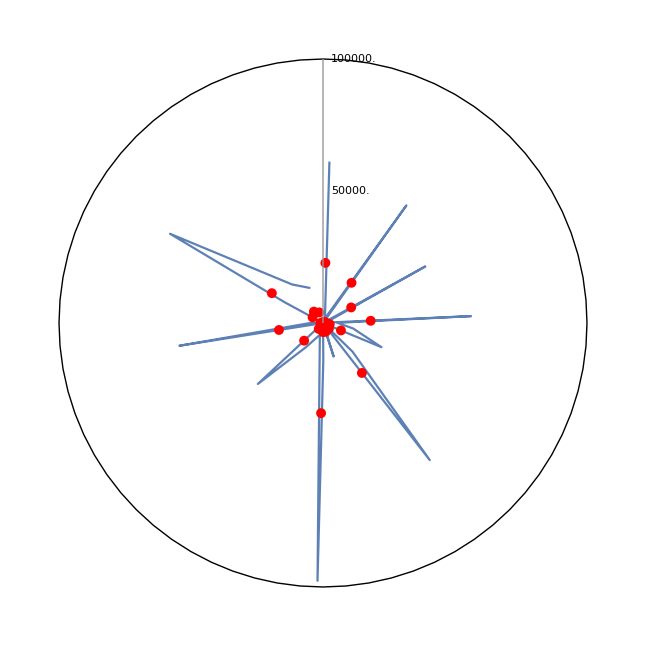

```mathematica
ListPolarPlot[{angleVisits2WD[[All,2;;3]],angleVisits2WE[[All,2;;3]]}, AspectRatio->1, Joined->{True,False}, PlotStyle->{Automatic,Red},PlotRange->Full, PolarAxes->True,PolarGridLines->{False,True}, PolarTicks->{angleTicks,{50000,100000}}, PlotRangeClipping->False]
```

```mathematica
Histogram[WeightedData[Mod[angleVisits[[All,2]],360],angleVisits[[All,3]]],30]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Histogram::ldata: WeightedData[Mod[Symbol[],360],Symbol[]] is not a valid dataset or list of datasets.

Histogram[WeightedData[Mod[Symbol[],360],Symbol[]],30]

```mathematica
commCodes[[1;;5]]//TableForm
```

COD_PRO | PRO_COM | COMUNE | COMUNE_CAPOLUOGO
1 | 1001 | Agliè | 0
1 | 1002 | Airasca | 0
1 | 1003 | Ala di Stura | 0
1 | 1004 | Albiano d'Ivrea | 0

```mathematica
findCommByName[#[[3]]]&/@commCodes[[1;;10]]
```

{{1,1,16},{13,6,1},{13,6,2},{13,6,3},{13,6,4},{13,6,5},{13,6,6},{13,6,7},{13,6,8},{13,6,9}}

```mathematica
italianDayOd[[All,-2]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
commCodes[[1;;50]]//TableForm
```

COD_PRO | PRO_COM | COMUNE | COMUNE_CAPOLUOGO
1 | 1001 | Agliè | 0
1 | 1002 | Airasca | 0
1 | 1003 | Ala di Stura | 0
1 | 1004 | Albiano d'Ivrea | 0
1 | 1005 | Alice Superiore | 0
1 | 1006 | Almese | 0
1 | 1007 | Alpette | 0
1 | 1008 | Alpignano | 0
1 | 1009 | Andezeno | 0
1 | 1010 | Andrate | 0
1 | 1011 | Angrogna | 0
1 | 1012 | Arignano | 0
1 | 1013 | Avigliana | 0
1 | 1014 | Azeglio | 0
1 | 1015 | Bairo | 0
1 | 1016 | Balangero | 0
1 | 1017 | Baldissero Canavese | 0
1 | 1018 | Baldissero Torinese | 0
1 | 1019 | Balme | 0
1 | 1020 | Banchette | 0
1 | 1021 | Barbania | 0
1 | 1022 | Bardonecchia | 0
1 | 1023 | Barone Canavese | 0
1 | 1024 | Beinasco | 0
1 | 1025 | Bibiana | 0
1 | 1026 | Bobbio Pellice | 0
1 | 1027 | Bollengo | 0
1 | 1028 | Borgaro Torinese | 0
1 | 1029 | Borgiallo | 0
1 | 1030 | Borgofranco d'Ivrea | 0
1 | 1031 | Borgomasino | 0
1 | 1032 | Borgone Susa | 0
1 | 1033 | Bosconero | 0
1 | 1034 | Brandizzo | 0
1 | 1035 | Bricherasio | 0
1 | 1036 | Brosso | 0
1 | 1037 | Brozolo | 0
1 | 1038 | Bruino | 0
1 | 1039 | Brusasco | 0
1 | 1040 | Bruzolo | 0
1 | 1041 | Buriasco | 0
1 | 1042 | Burolo | 0
1 | 1043 | Busano | 0
1 | 1044 | Bussoleno | 0
1 | 1045 | Buttigliera Alta | 0
1 | 1046 | Cafasse | 0
1 | 1047 | Caluso | 0
1 | 1048 | Cambiano | 0
1 | 1049 | Campiglione Fenile | 0

```mathematica
provCodes=Import[NotebookDirectory[]<>"codici_istat_provincia.csv"];
provCodes[[1;;5]]//TableForm
provNamesAss=AssociationThread[provCodes[[All,2]]->provCodes[[All,3]]];
provCodesVeneto=Select[provCodes,#[[1]]==5&];
```

COD_REG | COD_PRO | PROVINCIA | PROV_SIGLA
1 | 1 | Torino | TO
1 | 2 | Vercelli | VC
1 | 3 | Novara | NO
1 | 4 | Cuneo | CN

```mathematica
commCodes=Import[NotebookDirectory[]<>"codici_istat_comune.csv"];
commNames=Function[{province},Select[commCodes,#[[1]]==province[[2]]&][[All,3]]]/@provCodesVeneto;
```

```mathematica
provCodesVeneto
```

{{5,23,Verona,VR},{5,24,Vicenza,VI},{5,25,Belluno,BL},{5,26,Treviso,TV},{5,27,Venezia,VE},{5,28,Padova,PD},{5,29,Rovigo,RO}}

```mathematica
stupidReplacements={"Venezia"->"Venice","Padova"->"Padua"};
```

```mathematica
knownComms=(CanonicalName[#][[1]]&/@Entity["AdministrativeDivision",{#[[3]]/.stupidReplacements,"Veneto","Italy"}]["Subdivisions"])&/@provCodesVeneto;
```

```mathematica
commKnownNamesAss=MapThread[Function[{known,real},Association[{#->Nearest[known,#][[1]]}&/@real]],{knownComms,commNames}];
```

```mathematica
commEntis=MapThread[Function[{provName,commNames,knownNames},Entity["AdministrativeDivision",{#/.knownNames,provName/.stupidReplacements,"Veneto", "Italy"}]&/@commNames],{provCodesVeneto[[All,3]],commNames,commKnownNamesAss}];
```

```mathematica
GeoGraphics[Riffle[Polygon/@commEntis[[6]],Unevaluated@RandomColor[]],GeoBackground->"StreetMap", ImageSize->Large]
```

-Graphics-

```mathematica
28086/.commNamesAss
```

Selvazzano Dentro

### Distance Distribution

```mathematica
dayOdD[[1;;5]]//TableForm
```

DOW | CUST_CLASS | COD_COUNTRY | COD_PRO | PRO_COM | VISITORS
Mercoledì | visitor | 222 | 35 | 35033 | 968
Lunedì | visitor | 222 | 22 | 22098 | 64
Domenica | visitor | 222 | 52 | 52032 | 516
Giovedì | visitor | 222 | 108 | 108009 | 128

```mathematica
perCommAss=Total[#[[All,6]]]&/@GroupBy[italianDayOdD, #[[5]]&];
perComm=Partition[Riffle[Keys[perCommAss],Values[perCommAss]],2];
(*niceProvs=Select[perProvs,!NumberQ[#[[1]]/.provNamesAss] && #[[1]] ≠ ""&];*)
```

```mathematica
Dimensions@Values@distisPadAss
```

{7300,2}

```mathematica
perDist=Select[Partition[Riffle[(Keys[perCommAss]/.distisPadAss),Values[perCommAss]],2],Length@#[[1]]==2&];
perDistMIN=Partition[Flatten[perDist],3][[All,{1,3}]];
perDistMET=Partition[Flatten[perDist],3][[All,{2,3}]];
```

```mathematica
nlm=NonlinearModelFit[perDistMET,{a/r^(1/2)+b},{a,b,c},r]
```

FittedModel[-6820.84+(3.55506×10^6)/(√r)]

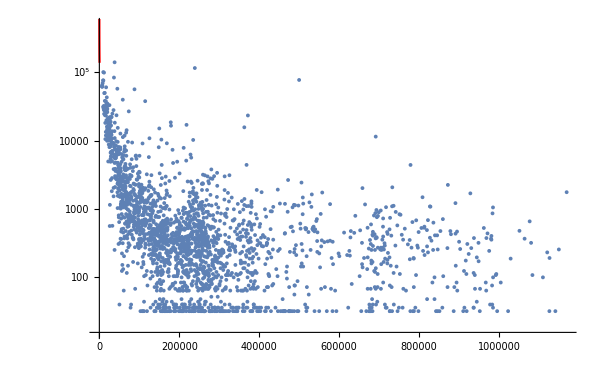

```mathematica
Show[ListLogPlot[SortBy[perDistMET,First], PlotRange->{All,{0,500000}}, ImageSize->600],LogPlot[nlm[x],{x,0,600}, PlotRange->All, PlotStyle->Red]]
```

```mathematica
ClearAll[BinListsBy]
BinListsBy[data_List,binspecs__List]:=Module[{fs,idata,len,out},len=Length[data];
fs={binspecs};
If[AllTrue[fs,MatchQ[#,{_,_?NumericQ,_?NumericQ}|{_,_?NumericQ,_?NumericQ,_?NumericQ}]&],idata=Table[Map[f,data],{f,fs[[All,1]]}];
AppendTo[idata,Range[len]];
out=BinLists[Transpose[idata],Sequence@@(Rest/@fs),{0,len+1,len+1}];
out=Part[out,Sequence@@ConstantArray[All,Length[fs]],1,All,-1];
Map[data[[#]]&,out,{Length[fs]}],Print["Your specification is incorrect…"];]]
BinListsBy::usage=Evaluate[Uncompress@"1:eJztlctqwkAUhn2DvsLpPoUYobelha66qkt1McmcmFPMTHDGSxBfuE/RXKiSRCSOgyi6mTAXPv6f85+cR19+D34fOp0+iS9SWvXT4Xr0/vny0S3Wt2J9Hcx9Fcwo0X25GpYXq+LjOlBuy+fuuHJ6JMOzwOg1GJ7rPW8cWIctgVQFxiRMZNUpbFWhbMbgk1BGFqlCAhKg5kGAStECs53GCc5Kuo96iSis+AYmuBXr4DOFHKQAHSEs2HSOCjiGJLJTP4WYJQmJCYSgJSALIpBh/jQeuV3vHtOzxtQBTnajWqCygnKCJXEd3TN6fRltBVMJBhZ8NTFNa7ksMOZVIzQG8cQpRqFICjbN8yrySmf1tdAA21j9B6gVMzzIbKus6bwGCuWszPLWfz3N54tzeoixcYyEGPVEeohhKKTZWMcL6dWEXMEAsZEeC+G5wSl0IX27GyEX0r8nCrLfxztBtz5sjQryY6EgTUZRiL29mOm8xEGe/Q1ykZxptmeo/wEBvbZm"];
```

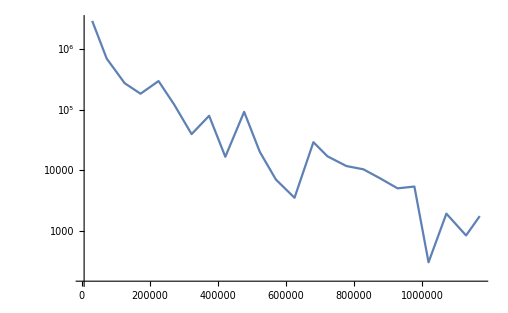

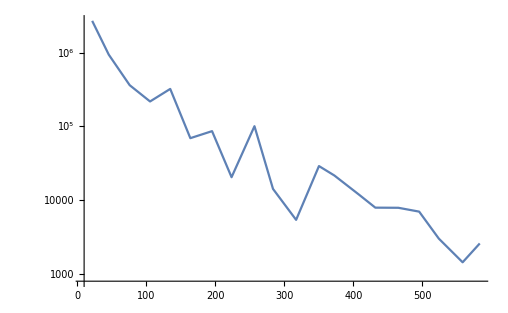

```mathematica
tmp={Mean[#[[All,1]]],Total[#[[All,2]]]}&/@BinListsBy[perDistMET,{First,0,10000000,50000}];
ListLogPlot[tmp, Joined->True, PlotRange->All]

tmp={Mean[#[[All,1]]],Total[#[[All,2]]]}&/@BinListsBy[perDistMIN,{First,0,600,30}];
ListLogPlot[tmp, Joined->True, PlotRange->All]
```

```mathematica
afs//Dimensions
```

{786,3}

```mathematica
Select[afs,#[[1]]==120 || #[[2]]==120&]
```

{{120,216,18942},{111,120,1662}}

```mathematica
af=Import[NotebookDirectory[]<>"Data/areaflow.csv"][[2;;-1]];
afs={#[[1,1]],#[[1,2]],Total@#[[All,3]]}&/@GatherBy[af,#[[1]]^2+#[[2]]^2&];
(*afs = RandomSample[afs,30];*)
```

```mathematica
afs={{1,2,1},{2,3,5},{3,1,2},{1,4,1},{2,4,1},{3,4,1}};
```

```mathematica
edges=MapThread[UndirectedEdge, {afs[[All,1]],afs[[All,2]]}];
flows=afs[[All,3]];
```

```mathematica
thick[v_]:=({mi,ma}=MinMax[flows]; Return@N[((v-mi)/(ma-mi+0.0001))])
styles = Directive[RGBColor[0.2,0.4,0.9,(thick[#]-0.0)*20],Thickness[Max[thick[#]/100,0.001]]]&/@flows;
```

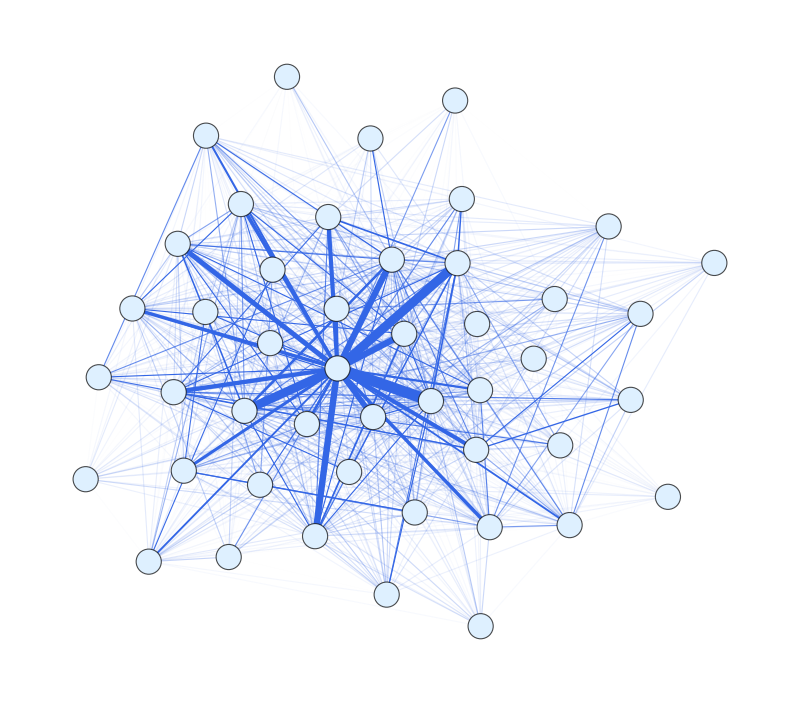

```mathematica
graph=GraphPlot[Graph[edges,EdgeWeight->1000/(0.001+thick/@flows),GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True,"MaxIteration"->500,"RepulsiveForcePower"->-30},VertexLabels->Automatic],ImageSize->800,EdgeStyle->Thread[edges->styles],VertexLabels->Placed["Name",Center],VertexSize->0.5,VertexStyle->LightBlue]
```

```mathematica
Export[NotebookDirectory[]<>"Data\graph_30.svg",graph]
```

C:\Users\Simon\Google Drive\Uni\Master\Machine Learning Lab\Python Course\LaboratoryOfComputationalPhysics-Group8\Data\graph_30.svg

```mathematica
styles[[1;;20]]
```

{Directive[RGBColor[0.2, 0.4, 0.9, 4.5391236129645485],Thickness[0.00226956]],Directive[RGBColor[0.2, 0.4, 0.9, 0.5204739385211641],Thickness[0.000260237]],Directive[RGBColor[0.2, 0.4, 0.9, 0.22489139523064972],Thickness[0.000112446]],Directive[RGBColor[0.2, 0.4, 0.9, 1.369418973722503],Thickness[0.000684709]],Directive[RGBColor[0.2, 0.4, 0.9, 0.6205013209727062],Thickness[0.000310251]],Directive[RGBColor[0.2, 0.4, 0.9, 0.4657682259522236],Thickness[0.000232884]],Directive[RGBColor[0.2, 0.4, 0.9, 0.6322535763243671],Thickness[0.000316127]],Directive[RGBColor[0.2, 0.4, 0.9, 0.3973712839118898],Thickness[0.000198686]],Directive[RGBColor[0.2, 0.4, 0.9, 0.10547427158178294],Thickness[0.0000527371]],Directive[RGBColor[0.2, 0.4, 0.9, 0.11667887775458811],Thickness[0.0000583394]],Directive[RGBColor[0.2, 0.4, 0.9, 0.07905389903428328],Thickness[0.0000395269]],Directive[RGBColor[0.2, 0.4, 0.9, 0.2769476698802611],Thickness[0.000138474]],Directive[RGBColor[0.2, 0.4, 0.9, 0.2982467825390017],Thickness[0.000149123]],Directive[RGBColor[0.2, 0.4, 0.9, 0.3327634821360713],Thickness[0.000166382]],Directive[RGBColor[0.2, 0.4, 0.9, 0.409759996417356],Thickness[0.00020488]],Directive[RGBColor[0.2, 0.4, 0.9, 0.5039556551805424],Thickness[0.000251978]],Directive[RGBColor[0.2, 0.4, 0.9, 0.7369285761316038],Thickness[0.000368464]],Directive[RGBColor[0.2, 0.4, 0.9, 0.04922922078038311],Thickness[0.0000246146]],Directive[RGBColor[0.2, 0.4, 0.9, 0.3619813058944827],Thickness[0.000180991]],Directive[RGBColor[0.2, 0.4, 0.9, 0.1441353433431662],Thickness[0.0000720677]]}

```mathematica
Quantile[flows]
```

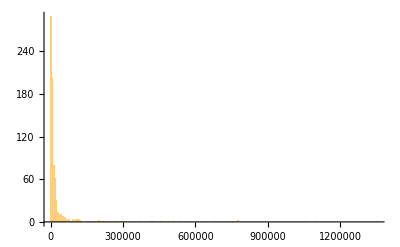

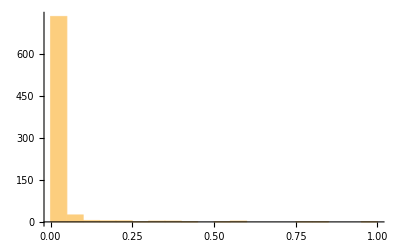

```mathematica
Histogram[flows, PlotRange->All]
Histogram[thick/@flows,15, PlotRange->Full]
```

```mathematica
MinMax[flows]
```

{32,681085}

```mathematica
lerp[x_]:=Interpolation[MinMax[flows], InterpolationOrder->1][1+x]
```

```mathematica
Lerp
```

```mathematica
Select[af,#[[2]]==209&]
```

{{101,209,1855},{102,209,1542},{103,209,32},{104,209,32},{105,209,252},{106,209,1486},{107,209,32},{108,209,136},{109,209,32}}